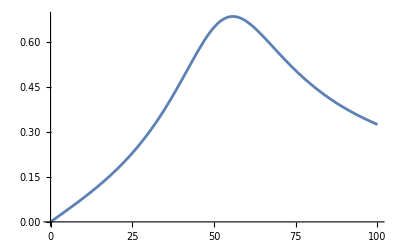

-Graphics-

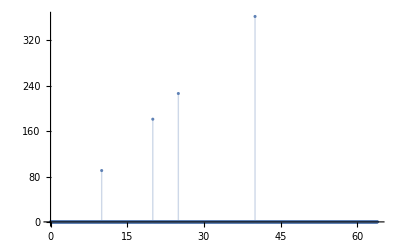

0.079350484192

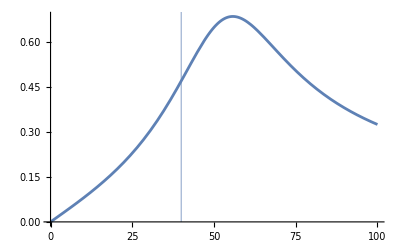

```mathematica
L1=SetPrecision[13.2111694517397,15];
L2=SetPrecision[0.524511360054314,15];
C1=SetPrecision[0.0000102992617837037,15];
C2=SetPrecision[0.0000143453621996884,13];
R1=SetPrecision[100.793558967849,15];
R2=SetPrecision[35.96448954979,15];
R3=SetPrecision[1054.70791442856,14];
R4=SetPrecision[538.353431816832,15];
dt=SetPrecision[0.0196349540849362,15];
N1=8192;
t=dt*N1;


(*передаточная функция и ее АЧХ*)
Z1[w_]=R4+1/(I w C2); 
Z2[w_]=1/(I w C1)+R2+I w L2+R3; 
Zparalel[w_]=1/(1/Z1[w]+1/Z2[w]); 
I1[w_]=Uin/(R1+I w L1+Zparalel[w]);
Upar[w_]=I1[w]*Zparalel[w];
Ipar1[w_]=Upar[w]/Z1[w];
Uout[w_]=Ipar1[w]*R4;
H[w_]=Uout[w]/Uin;
Plot[Abs@H[w],{w,0,100}]

(*сигнал*)
signal=ReadList["C:\\Users\\metro\\Downloads\\16.txt"];
ForPlot=Table[{(i-1)*dt,signal[[i]]},{i,1,N1}];
ListPlot[ForPlot,Filling->Axis,PlotRange->Full]

(*спектр*)
Fsig=Fourier[signal];
outN=Length@Fsig;
df=1/t;
FourAbs=Table[{2 π df (i-1),Abs@Fsig[[i]]},{i,1,outN/5}];
ListPlot[FourAbs,Filling->Axis,PlotRange->Full]


(*коэффициент усиления первой гармоники*)
Abs@H[10]
Show[Plot[Abs@H[w],{w,0,100}],ListPlot[{{40,3}},Filling->Axis]]
```